```mathematica
1.Naloga

trikotnik={{0,0},{0,5},{7,4}} (*(0,0)=A, (0,5)=B, (7,4)=C*)
stranice[{AA_,BB_,CC_}]:={{BB,CC},{CC,AA},{AA,BB}}
koti[{AA_,BB_,CC_}]:={{CC,AA,BB},{AA,BB,CC},{BB,CC,AA}}
```

```mathematica
stranice[trikotnik]
```

{{{0,0},{0,5}},{{0,5},{7,4}},{{7,4},{0,0}}}

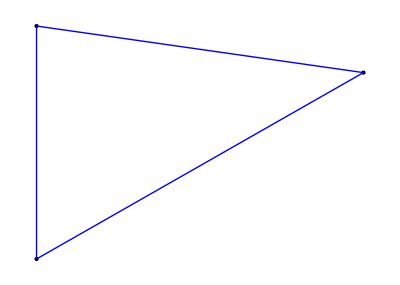

```mathematica
SlikaOglisc[trikotnik_] := Map[Point, trikotnik];
SlikaStranic[trikotnik_] := Map[Line, stranice[trikotnik]];
NarisiTrikotnik[trikotnik_] := Graphics[
{PointSize[Large], SlikaOglisc[trikotnik], {Blue, SlikaStranic[trikotnik]}}, AspectRatio -> Automatic
]
NarisiTrikotnik[trikotnik]
```

```mathematica
2. Naloga
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}]:= Normalize[Normalize[z-y]+Normalize[x-y]]
```

```mathematica
SimetralaKota[{x_, y_, z_}, dol_:10] := {y,VektorSimetraleKota[{x,y,z}]+y*dol}
```

```mathematica
3. Naloga
```

```mathematica
SlikaSimetralKotov[trikotnik_, dol_:10] := Map[Line, Map[SimetralaKota, koti[trikotnik]]];

NarisiTrikotnik[{x_,y_,z_}]:= Graphics[Line[SimetralaKota[{x,y,z},10]]]
```